```mathematica
Cor[x_,L_]:=((Exp[2L]-1)/(Exp[2L]-2Cos[2π*x]*Exp[L]+1))*0.1
```

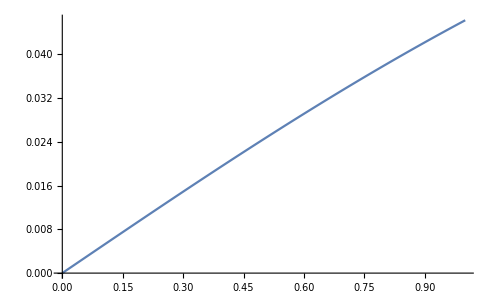

```mathematica
Plot[Cor[0.5,L],{L,0,1}]
```

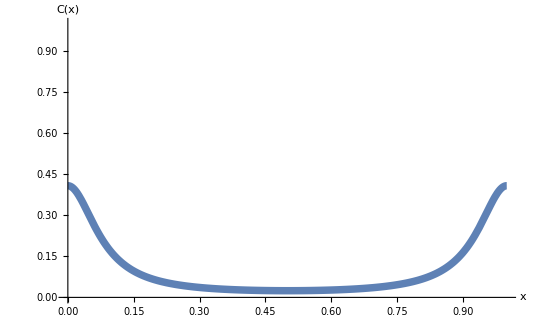

```mathematica
Plot[Cor[x,.5],{x,0,1},PlotRange->{{0,1},{0,1}},AxesLabel->{Style[x,Large],Style["C(x)",Large]},LabelStyle->Directive[Large, Black,Bold],PlotStyle->{Thickness[0.01]},AxesStyle->Thick]
```

```mathematica
Plot3D[Cor[x,L],{x,0,1},{L,0,1},AxesLabel->{Style[x,Large],Style[L,Large],Style["C(x,L)",Large]}]
```

-Graphics3D-